## Basic CR model

### Initialize constants

Set number of consumers, resources, and enzyme budget

```mathematica
m=5;
p=3;
enzymeBudget=1;
```

Define constants for each consumer

```mathematica
c=enzymeBudget*Normalize[#,Total]&/@RandomReal[{0,1},{m,p}]
```

{{0.422651,0.369224,0.208125},{0.463358,0.223856,0.312785},{0.226914,0.57244,0.200646},{0.661902,0.0399702,0.298128},{0.273796,0.668914,0.0572904}}

```mathematica
g=Table[1,m,p]
```

{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}

```mathematica
z=Table[0.1,m]
```

{0.1,0.1,0.1,0.1,0.1}

Define constants for each resource

```mathematica
κ=Table[0.3,p]
```

{0.3,0.3,0.3}

```mathematica
μ=Table[0,p]
```

{0,0,0}

### Initialize populations

```mathematica
r0=Table[1,p]
```

{1,1,1}

```mathematica
n0=Table[1,m]
```

{1,1,1,1,1}

### Solve The differential equations

```mathematica
sols=NDSolve[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
{r,n},
{t,0,10000}][[1]];
```

### Plot dynamics

```mathematica
sols
```

{r→InterpolatingFunction[…],n→InterpolatingFunction[…]}

```mathematica
Show[Plot3D[1-x-y,{x,0,1},{y,0,1},PlotStyle->Directive[Opacity[0.3]]],ListPointPlot3D[List/@c],ListPointPlot3DAspectRatio->1]
```

-Graphics3D-

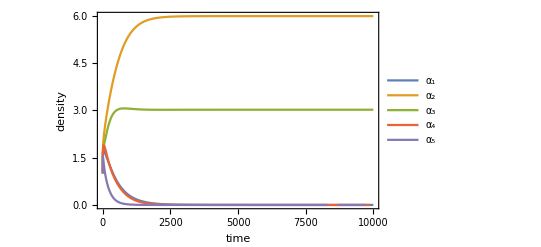

```mathematica
Plot[Evaluate[Table[Indexed[n[t],a]/.sols,{a,m}]],{t,0,10000},PlotRange->{All,{0,All}},Frame->True,FrameLabel->{"time","density"},PlotLegends->{"α_1","α_2","α_3","α_4","α_5"}]
```

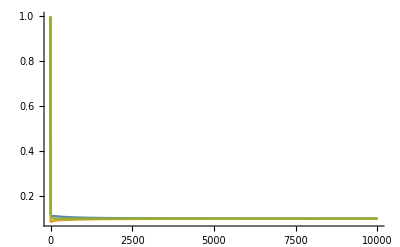

```mathematica
Plot[Evaluate[Table[Indexed[r[t],j]/.sols,{j,p}]],{t,0,10000},PlotRange->{All,{0,All}}]
```

### Equilibrium state

```mathematica
crSteadyState[{n0_,c_,g_,z_},r0_,κ_,μ_,tMax_:10000000]:=
NDSolveValue[{
r[0]==r0,
r'[t]==κ-μ*r[t]-r[t]*n[t].c,
n[0]==n0,
n'[t]==n[t]*(r[t].Transpose[c*g]-z)
},
n,
{t,0,tMax}][tMax]
```

```mathematica
crSteadyState[{n0,c,g,z},r0,κ,μ]
```

{-1.65143×10^-31,5.98281,3.01719,1.69795×10^-32,3.11682×10^-38}

## HGT

Mutate one of the vectors and change all the corresponding vectors

```mathematica
(*Input: each of the variables involving α 
Output: each of the updated variables*)
```

```mathematica
mutate[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0,p=Length[c[[1]]],mutation},
		mutation=ReplacePart[
			ConstantArray[0,p],
			RandomInteger[{1,p}]->RandomVariate[NormalDistribution[0,0.1]]];
		AppendTo[c,enzymeBudget*Normalize[Ramp[RandomChoice[Ramp[n]->c]+mutation],Total]];
		AppendTo[n,0.1];
		AppendTo[g,Table[1,p]];
		AppendTo[z,0.1];
		{n,c,g,z}
	]
```

```mathematica
mutate[{n0,c,g,z}]
```

{{1,1,1,1,1,0.1},{{0.422651,0.369224,0.208125},{0.463358,0.223856,0.312785},{0.226914,0.57244,0.200646},{0.661902,0.0399702,0.298128},{0.273796,0.668914,0.0572904},{0.421699,0.368391,0.20991}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}},{0.1,0.1,0.1,0.1,0.1,0.1}}

## The whole enchilada

```mathematica
oneStep[{n0_,c0_,g0_,z0_}]:=
	Module[{n=n0,c=c0,g=g0,z=z0},
		{n,c,g,z}=mutate[{n,c,g,z}];
		n=crSteadyState[{n,c,g,z},r0,κ,μ];
		{n,c,g,z}]
```

```mathematica
run=NestList[oneStep,{n0,c,g,z},100];
```

```mathematica
Count[0]/@Chop[run[[All,1]]]
```

{0,4,5,6,7,8,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10}

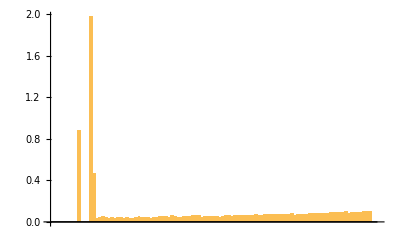

```mathematica
BarChart[run[[-1,1]]]
```